# UCI Panmictic

## Functions

```mathematica
ReadDataset[path_,thresholds_]:=Module[{raw,clean,expTuples},
raw=Import[path];
clean=#[[1;;(1+Length[thresholds])]]&/@raw;
expTuples={GetExperimentID[#[[1]]],#[[2;;All]]}&/@clean;
expTuples//Sort
]
GetExperimentID[expStr_]:=ToExpression[#]&/@StringSplit[expStr,"_"][[2;;All]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
ColorBlend[a_]:=Blend[{{0,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},a]
ColorBlendCost[a_]:=Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0.3764705882352941, 0., 0.7098039215686275],Opacity[1]]}},a]
ColorBlendSensitivity[a_]:=Blend[{{-1,Directive[RGBColor[0, 0, 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[1, 0., 1],Opacity[1]]}},a]
weeksRanges={{8,12},{12, 24},{24, 52},{52,1.5*52}};
(*colorsSolid=hexToRGB[#]&/@{"#6000b5","#0a4afc","#268cff","#75c1ff", "#c6ebff"};*)
(*colorsSolid={RGBColor[1, 0, 0],RGBColor[1, 0.56, 1],RGBColor[0, 0.8, 1],RGBColor[0.0006103608758678569, 0., 0.9347219043259327]};*)
colorsSolid={RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0]};
ColorBlendA[a_]:=Blend[{{1,Directive[colorsSolid[[1]],Opacity[0]]},{0,Directive[colorsSolid[[1]],Opacity[0]]}},a];
ColorBlendB[a_]:=Blend[{{1,Directive[colorsSolid[[2]],Opacity[0]]},{0,Directive[colorsSolid[[2]],Opacity[0]]}},a];
ColorBlendC[a_]:=Blend[{{1,Directive[colorsSolid[[3]],Opacity[0]]},{0,Directive[colorsSolid[[3]],Opacity[0]]}},a];
ColorBlendD[a_]:=Blend[{{1,Directive[colorsSolid[[4]],Opacity[0]]},{0,Directive[colorsSolid[[4]],Opacity[0]]}},a];
ColorBlendX[a_]:=Blend[{{1,Directive[colorsSolid[[4]],Opacity[0]]},{0,Directive[colorsSolid[[4]],Opacity[0]]}},a];
colors={ColorBlendA,ColorBlendB,ColorBlendC,ColorBlendD};
```

```mathematica
hexToRGB[#]&/@{"#6000b5","#0a4afc","#268cff","#75c1ff", "#c6ebff"}
```

{RGBColor[0.3764705882352941, 0., 0.7098039215686275],RGBColor[0.0392156862745098, 0.2901960784313725, 0.9882352941176471],RGBColor[0.14901960784313725, 0.5490196078431373, 1.],RGBColor[0.4588235294117647, 0.7568627450980392, 1.],RGBColor[0.7764705882352941, 0.9215686274509803, 1.]}

## Load Data

```mathematica
SetDirectory["/Users/sanchez.hmsc/Desktop/panmictic/islandGravidFemales/"];
{thresholds,POPSIZE}={{.25,.50,.75,.90,.95},1000000};
(*Load Data*)
expTuples=ReadDataset["./thresholdCrosses.csv",thresholds];
paramsRanges=DeleteDuplicates[#]&/@(expTuples[[All,1]]//Transpose)
(* Key: {releaseRatio, releasePattern, fitnessCost, standingVariation}*)
```

{{100,133,200,400,571,1000,1333,2000,4000,10000,20000,40000,100000,250000,500000,1000000},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53},{100},{1,5,10,50,100,500,1000}}

```mathematica
1/100000//N
```

0.00001

## Export Legend

```mathematica
range=Length[Range[Last[weeksRanges][[2]]-First[weeksRanges[[1]]]]-1];
labels=Range[weeksRanges[[1]],Last[weeksRanges][[2]],2];
blends=ColorBlend[#]&/@Range[0,1,1/range];
colorScale=Transpose[{
Reverse[ImageResize[Rasterize[#]//ImageCrop,50]&/@blends],
Reverse[Style[ToString[#],30]&/@Range[Min[weeksRanges//Flatten],Max[weeksRanges//Flatten]]]
}][[;;;;2]]//Grid;
Export["./img/legend.pdf",colorScale]
(**)
bar=BarLegend[{ColorBlend[#]&,{0,1}}
,LabelStyle->{FontSize->.001}
];
Export["./img/barLegend.pdf",bar]
```

./img/legend.pdf

./img/barLegend.pdf

## Export Response Curves

```mathematica
Table[
Table[
trends=Table[
{thresholdIx,releases,standingVar}={j,rel,svar};
filtered=Cases[expTuples,{{_,releases,_,standingVar},_}];
tuples={#[[1,1]]/1000000,#[[2,thresholdIx]]/365}&/@filtered
,{rel,paramsRanges[[2]]}];
linePlot=ListLogLogPlot[trends
,AspectRatio->1
,Epilog->Flatten[{PointSize[Medium],Opacity[1],(Point[#]&/@tuples)}]
,Frame->True
(*,FrameLabel->(Style[#,30]&/@{
"Release Fraction", 
"Years to "<>ToString[thresholds[[thresholdIx]]]
})*)
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicks->None
,FrameTicksStyle->Directive[20]
,GridLines->{Range[0,1,.1],{.1,.2,.5,1,2,5}}
,ImageSize->800
,InterpolationOrder->2
,Joined->True
(*,PlotLabel->Style["Standing Variation: "<>ToString[(standingVar/100000)//N],30]*)
,PlotMarkers->{None, 10}
,PlotRange->{{10^-4,1},{0.05,5}}
,PlotStyle->({Thickness[.006],ColorBlend[#]}&/@Range[0,1,1/Length[paramsRanges[[2]]]])
];
Export[
"./img/CR"<>"_"<>
StringPadLeft[ToString[Round[thresholds[[thresholdIx]]*1000]],4,"0"]<>
"_"<>StringPadLeft[ToString[standingVar],4,"0"]<>".pdf"
,linePlot
,ImageResolution-> 750
]
,{svar,paramsRanges[[-1]]}]
,{j,1,5}]
```

{{./img/CR_0250_0001.pdf,./img/CR_0250_0005.pdf,./img/CR_0250_0010.pdf,./img/CR_0250_0050.pdf,./img/CR_0250_0100.pdf,./img/CR_0250_0500.pdf,./img/CR_0250_1000.pdf},{./img/CR_0500_0001.pdf,./img/CR_0500_0005.pdf,./img/CR_0500_0010.pdf,./img/CR_0500_0050.pdf,./img/CR_0500_0100.pdf,./img/CR_0500_0500.pdf,./img/CR_0500_1000.pdf},{./img/CR_0750_0001.pdf,./img/CR_0750_0005.pdf,./img/CR_0750_0010.pdf,./img/CR_0750_0050.pdf,./img/CR_0750_0100.pdf,./img/CR_0750_0500.pdf,./img/CR_0750_1000.pdf},{./img/CR_0900_0001.pdf,./img/CR_0900_0005.pdf,./img/CR_0900_0010.pdf,./img/CR_0900_0050.pdf,./img/CR_0900_0100.pdf,./img/CR_0900_0500.pdf,./img/CR_0900_1000.pdf},{./img/CR_0950_0001.pdf,./img/CR_0950_0005.pdf,./img/CR_0950_0010.pdf,./img/CR_0950_0050.pdf,./img/CR_0950_0100.pdf,./img/CR_0950_0500.pdf,./img/CR_0950_1000.pdf}}

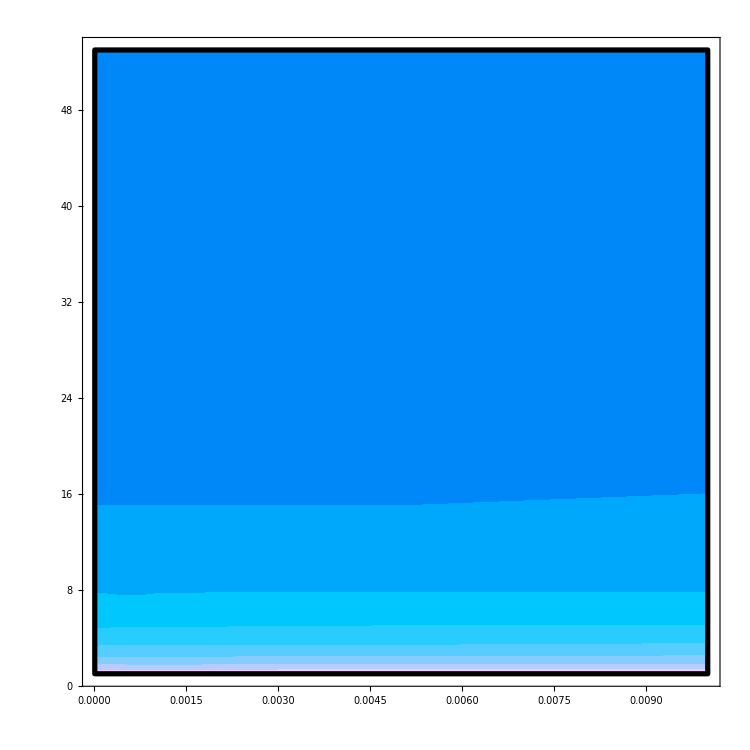

```mathematica
Clear[svar]
{ratio,thIx}={100,1};
filtered=Cases[expTuples,{{ratio,rel_,_,svar_},out_}->{rel,svar,out}];
shpd={#[[2]]/100000//N,#[[1]],#[[3,thIx]]/7}&/@filtered;
ListContourPlot[shpd
,BoundaryStyle->Directive[{Black, Thickness[.005]}]
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0],RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0]}
,ColorFunction->(ColorBlend[Rescale[#,{2,75}, {-1,1}]]&)
,ColorFunctionScaling->False
,ContourStyle->Directive[{Black, Opacity[0]}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->Automatic
,ImageSize->750
,InterpolationOrder->2
,Mesh->False
,MeshStyle->Directive[White, Opacity[.25]]
,PlotLegends->None
,PlotRange->All
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
]
```

## Explore Response Curves

```mathematica
Table[
trends=Table[
{thresholdIx,releases,standingVar}={2,rel,svar};
filtered=Cases[expTuples,{{_,releases,_,standingVar},_}];
tuples={#[[1,1]]/1000000,#[[2,thresholdIx]]/365}&/@filtered
,{rel,paramsRanges[[2]]}];
linePlot=ListLogLogPlot[trends
,AspectRatio->1
,Epilog->Flatten[{PointSize[Medium],Opacity[1],(Point[#]&/@tuples)}]
,Frame->True
(*,FrameLabel->(Style[#,30]&/@{
"Release Fraction", 
"Years to "<>ToString[thresholds[[thresholdIx]]]
})*)
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicks->{Range[0,1,.3], Range[0,5]}
,FrameTicksStyle->Directive[20]
,GridLines->{Range[0,1,.1],{.1,.2,.5,1,2,5}}
,ImageSize->800
,InterpolationOrder->1
,Joined->True
(*,PlotLabel->Style["Standing Variation: "<>ToString[(standingVar/100000)//N],30]*)
,PlotMarkers->{None, 10}
,PlotRange->{{10^-4,1},{0.05,5}}
,PlotStyle->({Thickness[.006],ColorBlend[#]}&/@Range[0,1,1/Length[paramsRanges[[2]]]])
]
,{svar,paramsRanges[[-1]]}];
```

## Export Response Surfaces

```mathematica
Table[
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
yLabels=DeleteDuplicates[{Log[N[#[[1,2]]]],N[#[[1,2]]]}&/@filtered][[2;; ;;4]];
xLabels=DeleteDuplicates[{Log[N[#[[1,1]]]/1000000],NumberForm[N[#[[1,1]]]/1000000,{1,4}]}&/@filtered][[2;; ;;4]];
(**)
cf=Table[
ListDensityPlot[tuples
,BoundaryStyle->Directive[{Black, Thickness[.005]}]
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0],RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0]}
,ColorFunction->(colors[[i]][#]&)
,ColorFunctionScaling->True
,Epilog->Flatten[{PointSize[Medium],Opacity[.2],(Point[#[[1;;2]]]&/@tuples)}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->2
,Mesh->False
,MeshStyle->Directive[White, Opacity[.25]]
,PlotLegends->None
,PlotRange->{All,All,weeksRanges[[i]]}
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
]
,{i,1,Length[weeksRanges]}];
ca=ListContourPlot[tuples
,ClippingStyle->{White,White}
,Contours->50
,ContourStyle->Directive[{Black, Opacity[0]}]
,ColorFunction->(ColorBlend[#/weeksRanges[[-1,2]]]&)
,ColorFunctionScaling->False
,Epilog->Flatten[{
PointSize[.0025],Opacity[1],(Point[#[[1;;2]]]&/@tuples),
White,Dashing[.01],Thickness[.0035],
Line[{{-4.605170185988091,10},{-4.605170185988091,24}}],
Line[{{-6.907755278982137,10},{-6.907755278982137,24}}],
Line[{{-4.605170185988091, 10},{-6.907755278982137,10}}],
Line[{{-4.605170185988091, 24},{-6.907755278982137,24}}]
}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->1
,Mesh->None
,MeshStyle->Directive[ White, Opacity[.25]]
,PlotLegends->None
,PlotRange->{All,{1,30},{Min[weeksRanges//Flatten],Max[weeksRanges//Flatten]}}
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
];
cfFull=Show[ca,cf];
Export[
"./img/RSS_"<>StringPadRight[ToString[thresholds[[thresholdIx]]*100],2,"0"]<>".png"
,cfFull
,ImageResolution->500
]
,{i,1,5}]
```

{./img/RSS_25.png,./img/RSS_50.png,./img/RSS_75.png,./img/RSS_90.png,./img/RSS_95.png}

## Explore Response Surfaces

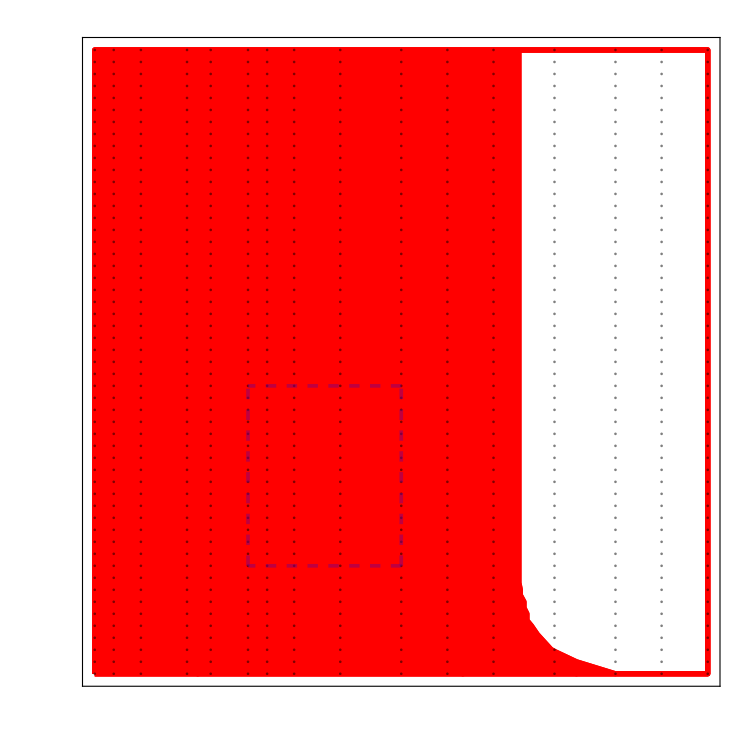

```mathematica
i=1;
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
yLabels=DeleteDuplicates[{Log[N[#[[1,2]]]],N[#[[1,2]]]}&/@filtered][[2;; ;;4]];
xLabels=DeleteDuplicates[{Log[N[#[[1,1]]]/1000000],NumberForm[N[#[[1,1]]]/1000000,{1,4}]}&/@filtered][[2;; ;;4]];
(**)
cf=Table[
ListDensityPlot[tuples
,BoundaryStyle->Directive[{Black, Thickness[.005]}]
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0],RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0]}
,ColorFunction->(colors[[i]][#]&)
,ColorFunctionScaling->True
,Epilog->Flatten[{PointSize[Medium],Opacity[.2],(Point[#[[1;;2]]]&/@tuples)}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->2
,Mesh->False
,MeshStyle->Directive[White, Opacity[.25]]
,PlotLegends->None
,PlotRange->{All,All,weeksRanges[[i]]}
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
]
,{i,1,Length[weeksRanges]}];
ca=ListContourPlot[tuples
,ClippingStyle->{White,White}
,Contours->50
,ContourStyle->Directive[{Black, Opacity[0]}]
,ColorFunction->(ColorBlend[#/weeksRanges[[-1,2]]]&)
,ColorFunctionScaling->False
,Epilog->Flatten[{
PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples),
Purple,Dashing[.01],Thickness[.0035],
Line[{{-4.605170185988091,10},{-4.605170185988091,25}}],
Line[{{-6.907755278982137,10},{-6.907755278982137,25}}],
Line[{{-4.605170185988091, 10},{-6.907755278982137,10}}],
Line[{{-4.605170185988091, 25},{-6.907755278982137,25}}]
}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->1
,Mesh->None
,MeshStyle->Directive[ White, Opacity[.25]]
,PlotLegends->None
,PlotRange->{All,All,{Min[weeksRanges//Flatten],Max[weeksRanges//Flatten]}}
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
];
cfFull=Show[ca,cf]
```

## Releases Optimization

```mathematica
{thresholdIx,standingVar}={4,100};
(*Time to Thresholds*)
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuplesTime={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
(*Releases*)
relSizes=Tuples[{paramsRanges[[1]]/1000000*POPSIZE//N,paramsRanges[[2]]}];
relMosquitos={#[[1]],#[[2]],#[[1]]*#[[2]]}&/@relSizes;
tuplesReleases={Log[N[#[[1]]]/1000000],#[[2]],Log[N[#[[3]]]]}&/@relMosquitos;
(*Cost*)
cost={#[[1,1]],#[[1,2]],#[[1,3]]/#[[2,3]]}&/@({tuplesReleases,tuplesTime}//Transpose);
```

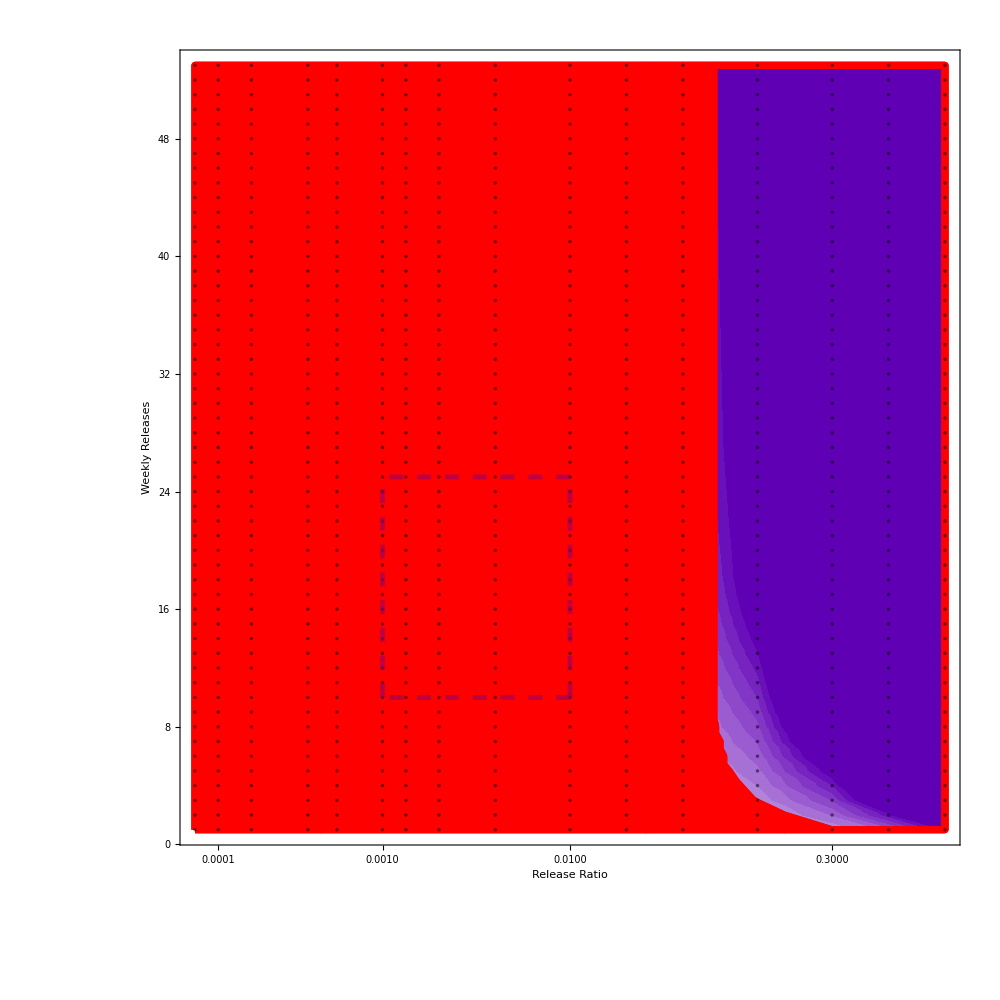

```mathematica
yLabels=DeleteDuplicates[{Log[N[#[[1,2]]]],N[#[[1,2]]]}&/@filtered][[2;; ;;4]];
xLabels=DeleteDuplicates[{Log[N[#[[1,1]]]/1000000],NumberForm[N[#[[1,1]]]/1000000,{1,4}]}&/@filtered][[2;; ;;4]];
cf=Table[
ListDensityPlot[tuples
,BoundaryStyle->Directive[{Black, Thickness[.005]}]
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0],RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0]}
,ColorFunction->(colors[[i]][#]&)
,ColorFunctionScaling->True
,Epilog->Flatten[{PointSize[Medium],Opacity[.2],(Point[#[[1;;2]]]&/@tuples)}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->2
,Mesh->False
,MeshStyle->Directive[White, Opacity[.25]]
,PlotLegends->None
,PlotRange->{All,All,weeksRanges[[i]]}
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
]
,{i,1,Length[weeksRanges]}];
ca=ListContourPlot[cost
,ClippingStyle->{White,White}
,Contours->50
,ContourStyle->Directive[{Black, Opacity[0]}]
,ColorFunction->(ColorBlendCost[#*1.5]&)
,ColorFunctionScaling->False
,Epilog->Flatten[{
PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples),
Purple,Dashing[.01],Thickness[.0035],
Line[{{-4.605170185988091,10},{-4.605170185988091,25}}],
Line[{{-6.907755278982137,10},{-6.907755278982137,25}}],
Line[{{-4.605170185988091, 10},{-6.907755278982137,10}}],
Line[{{-4.605170185988091, 25},{-6.907755278982137,25}}]
}]
,FrameLabel->(Style[#,50]&/@{"Release Ratio","Weekly Releases"})
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
(*,FrameTicks->Automatic*)
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->1000
,InterpolationOrder->1
,Mesh->None
,MeshStyle->Directive[ White, Opacity[.25]]
(*,PlotLabel->Style["Weeks to: "<>ToString[thresholds[[thresholdIx]]],50,Black]*)
,PlotLegends->None
,PlotRange->{All,All,All}(*{0, 260}}*)
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
];
cfFull=Show[ca,cf]
```

## Interpolations

```mathematica
i=3;
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={N[#[[1,1]]]/1000000,#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
```

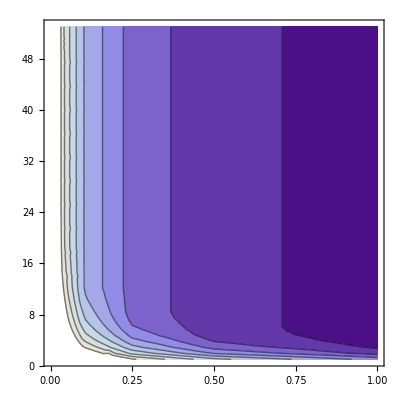

```mathematica
inputTriplets={{#[[1]],#[[2]]},#[[3]]}&/@tuples;
fInter=Interpolation[inputTriplets,Method->"Spline", InterpolationOrder->1];
ContourPlot[
fInter[x,y]
,{x,10^-4,1},{y,1,53}
,ColorFunction->"LakeColors"
]
```

```mathematica
ListPlot3D[tuples
,ColorFunction->"LakeColors"
,ImageSize->1500
,InterpolationOrder->0
,PlotRange->{{0,.1},{0,53},{0,80}}
]
```

-Graphics3D-

0.0821636

{0.0854217,12.5556}

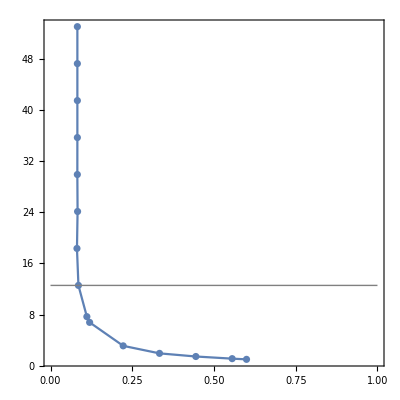

```mathematica
inputTriplets={{#[[1]],#[[2]]},#[[3]]}&/@tuples;
fInter=Interpolation[inputTriplets,Method->"Spline", InterpolationOrder->2];
region=ImplicitRegion[fInter[x,y]==15,{x,y}];
rp=RegionPlot[region,PlotRange->{{10^-4,1},{1,53}}];
pts=rp[[1,1,1]]//Sort;
quant=Quantile[pts[[All,1]],.25]
break=Sort[Cases[pts,{a_,b_}/;a<quant*1.05],#1[[2]]>#2[[2]]&][[-1]]
Show[{rp,pts//ListPlot}
,Epilog->{Gray,Line[{{0,break[[2]]},{1,break[[2]]}}]}
]
```

{{8,6.77778},{9,12.5556},{10,12.5556},{11,12.5556},{12,12.5556},{13,12.5556},{14,12.5556},{15,12.5556},{16,18.3333},{17,18.3333},{18,18.3333},{19,18.3333},{20,18.3333}}

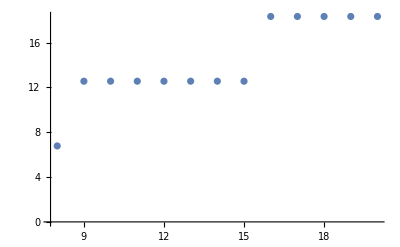

```mathematica
sweep=Table[
region=ImplicitRegion[fInter[x,y]==i,{x,y}];
rp=RegionPlot[region,PlotRange->{{10^-4,1},{1,53}}];
pts=rp[[1,1,1]]//Sort;
quant=Quantile[pts[[All,1]],.25];
break=Sort[Cases[pts,{a_,b_}/;a<quant*1.05],#1[[2]]>#2[[2]]&][[-1]];
{i,break[[2]]}
,{i,8,20}]
ListPlot[sweep]
```

## Compare Responses Export

```mathematica
(**)
SetDirectory["/Users/sanchez.hmsc/Desktop/panmictic/"];
{base,probe}={"island","islandGravidFemales"};
{dataA,dataB}={
ReadDataset["./"<>base<>"/thresholdCrosses.csv",thresholds],
ReadDataset["./"<>probe<>"/thresholdCrosses.csv",thresholds]
};
range=20;
```

```mathematica
Table[
transposedDatasets=({dataA,dataB}//Transpose);
diff={#[[1,1]],#[[2,2]]-#[[1,2]]}&/@transposedDatasets;
{thresholdIx,standingVar}={i,100};
filtered=Cases[diff,{{_,_,_,standingVar},_}];
tuples={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
(**)
lp=ListContourPlot[tuples
,Contours->50
,ContourStyle->Directive[{Black, Opacity[0]}]
,ClippingStyle->{RGBColor[0, 0, 0, 0.15],RGBColor[0, 0, 0, 0.15]}
,ColorFunction->(ColorBlendSensitivity[#/range]&)
,ColorFunctionScaling->False
,Epilog->Flatten[{PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples)}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->0
,Mesh->None
,MeshStyle->Directive[ White, Opacity[.25]]
,PlotLegends->None
,PlotRange->{All,All,{-range,range}}
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
];
(*Weeks Lines*)
expTuples=ReadDataset["./"<>base<>"/thresholdCrosses.csv",thresholds];
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuplesBase={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
{minQ,maxQ}=Quantile[Flatten[(#[[-1]]&/@diff)],{.1,.8}];
cf=Table[
ListDensityPlot[tuplesBase
,BoundaryStyle->Directive[{Black, Thickness[.005]}]
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0],RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0]}
,ColorFunction->(colors[[i]][#]&)
,InterpolationOrder->2
,PlotRange->{All,All,weeksRanges[[i]]}
]
,{i,1,Length[weeksRanges]}]//Show;
cfFull=Show[lp,cf];
Export[
"./img/SA"<>"_"<>StringPadLeft[ToString[Round[thresholds[[thresholdIx]]*1000]],4,"0"]<>"_"<>StringPadLeft[ToString[standingVar],4,"0"]<>"_"<>probe<>"_"<>base<>".pdf"
,cfFull
,ImageResolution-> 750
]
,{i,1,5}]
```

{./img/SA_0250_0100_islandGravidFemales_island.pdf,./img/SA_0500_0100_islandGravidFemales_island.pdf,./img/SA_0750_0100_islandGravidFemales_island.pdf,./img/SA_0900_0100_islandGravidFemales_island.pdf,./img/SA_0950_0100_islandGravidFemales_island.pdf}

## Compare Responses Explore

/Users/sanchez.hmsc/Desktop/panmictic

-0.857143

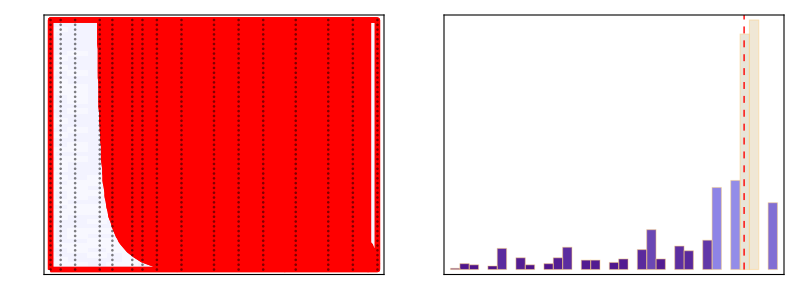

```mathematica
{i,range}={4,20};
(**)
SetDirectory["/Users/sanchez.hmsc/Desktop/panmictic/"]
{base,probe}={"island","islandGravidFemales"};
{dataA,dataB}={
ReadDataset["./"<>base<>"/thresholdCrosses.csv",thresholds],
ReadDataset["./"<>probe<>"/thresholdCrosses.csv",thresholds]
};
{thresholdIx,standingVar}={i,100};
(*Weeks Lines*)
expTuples=ReadDataset["./"<>base<>"/thresholdCrosses.csv",thresholds];
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuplesBase={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
cf=Table[
ListDensityPlot[tuplesBase
,BoundaryStyle->Directive[{Black, Thickness[.005]}]
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0],RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0]}
,ColorFunction->(colors[[i]][#]&)
,InterpolationOrder->2
,PlotRange->{All,All,weeksRanges[[i]]}
]
,{i,1,Length[weeksRanges]}]//Show;
(*Full Set*)
transposedDatasets=({dataA,dataB}//Transpose);
diff={#[[1,1]],#[[2,2]]-#[[1,2]]}&/@transposedDatasets;
{thresholdIx,standingVar}={i,100};
filtered=Cases[diff,{{_,_,_,standingVar},_}];
tuples={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
lp=ListContourPlot[tuples
,ClippingStyle->{RGBColor[0, 0, 0, 0.15],RGBColor[0, 0, 0, 0.15]}
,Contours->100
,ContourStyle->Directive[{Black, Opacity[0]}]
,ColorFunction->(ColorBlendSensitivity[#/range]&)
,ColorFunctionScaling->False
,Epilog->Flatten[{PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples)}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
(*,FrameTicks->{{Automatic,None},{xLabels,None}}*)
,ImageSize->750
,InterpolationOrder->0
,Mesh->None
,MeshStyle->Directive[ White, Opacity[.25]]
,PlotLegends->None
,PlotRange->{All,All,{-range,range}}
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
];
cfFull=Show[lp,cf];
(*Histogram*)
data=tuples[[All,-1]]//Flatten;
mean=Median[data]
gd=Histogram[data
,AspectRatio->1
,ColorFunction->"LakeColors"
,ColorFunctionScaling->True
,Frame->True
,FrameTicks->{{None,None},{Range[-100,100,5],None}}
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,ImageSize->750
,PlotRange->All
,Epilog->{Dashed,Line[{{0,0},{0,10000}}],Red,Line[{{mean,0},{mean,10000}}]}
];
Grid[{{cfFull,gd}}]
```

12

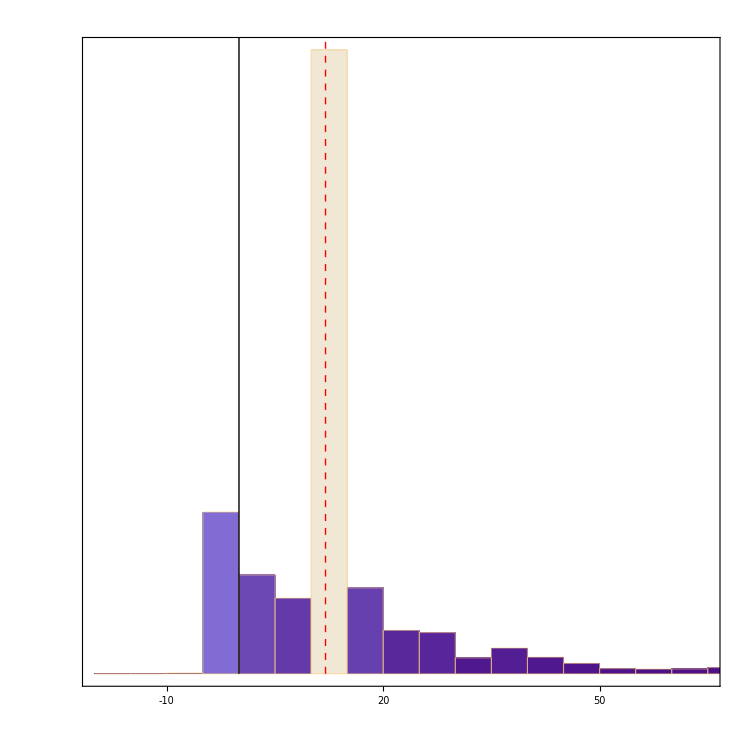

```mathematica
data=diff[[All,-1]]//Flatten;
mean=Median[data]
gd=Histogram[data
,AspectRatio->1
,ColorFunction->"LakeColors"
,Frame->True
,FrameTicks->{{None,None},{Range[-100,100,10],None}}
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,ImageSize->750
,Epilog->{Line[{{0,0},{0,2*10000}}],Dashed, Red,Line[{{mean,0},{mean,2*10000}}]}
]
```

```mathematica
SetDirectory["/Volumes/marshallShare/UCI/Yoosook/tParams/"]
{base,probe}={"island","islandMixed"};
{dataA,dataB}={
ReadDataset["./"<>base<>"/thresholdCrosses.csv",thresholds],
ReadDataset["./"<>probe<>"/thresholdCrosses.csv",thresholds]
};
```

/Volumes/marshallShare/UCI/Yoosook/tParams

```mathematica
Complement[dataA[[All,1]],dataB[[All,1]]]
```

{}

```mathematica
Length[dataA]
Length[dataB]
```

5936

5936

## Time Series

```mathematica
i=1;
{thresholdIx,standingVar}={i,100};
releases=10;
filtered=Cases[expTuples,{{_,releases,_,standingVar},_}];
tuples={N[#[[1,1]]]/1000000,#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
yLabels=DeleteDuplicates[{Log[N[#[[1,2]]]],N[#[[1,2]]]}&/@filtered][[2;; ;;4]];
xLabels=DeleteDuplicates[{Log[N[#[[1,1]]]/1000000],NumberForm[N[#[[1,1]]]/1000000,{1,4}]}&/@filtered][[2;; ;;4]];
```

```mathematica
tuples
```

{{0.0001,10,49.},{0.000133,10,47.1429},{0.0002,10,44.1429},{0.0004,10,39.2857},{0.000571,10,36.8571},{0.001,10,32.8571},{0.001333,10,30.8571},{0.002,10,27.8571},{0.004,10,23.},{0.01,10,16.4286},{0.02,10,12.},{0.04,10,8.85714},{0.1,10,5.85714},{0.25,10,4.14286},{0.5,10,3.28571},{1.,10,2.85714}}